```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Loading 9990 seeds from TargetScanHuman database, ver.7.1[*)
```

```mathematica
seeds=Import["miR_Family_Info.txt","Table"][[2;;,2]];
```

```mathematica
Length[seeds]
```

9990

```mathematica
lett=Flatten[Table[StringPartition[seeds[[ii]],1,1],{ii,1,Length[seeds]}],1];
```

```mathematica
p["A"]:="U";
p["U"]:="A";
p["C"]:="G";
p["G"]:="C";
```

```mathematica
pseeds=Table[StringJoin[Reverse[p[#1]&/@StringPartition[seeds[[ii]],1,1]]],{ii,1,Length[seeds]}];
```

```mathematica
up=Complement[Flatten[Outer[List,{"A","U","C","G"},{"A","U","C","G"}],1],{{"U","A"},{"A","U"},{"C","G"},{"G","C"}}]
```

{{A,A},{A,C},{A,G},{C,A},{C,C},{C,U},{G,A},{G,G},{G,U},{U,C},{U,G},{U,U}}

```mathematica
(** Command line to run RNAcofold.  Before running, you first need to install ViennaRNA package (ver.2.3) on your system **)
```

```mathematica
comm="RNAcofold --noPS -d2 --noLP -T 25 <<<'";
```

```mathematica
NSEED=10;
```

```mathematica
(** Loop over seeds of length 7, adding all possible dangling end combos.  The loop at the end is over NSEED random seeds chosen from the database.  You can increase NSEED to get more and more converged histograms,but this may be computationally expensive. **)
```

```mathematica
AbsoluteTiming[SetSharedVariable[ktab7,ktab7i];
ktab7={};
ktab7i={};
ParallelDo[
AppendTo[ktab7,Exp[ToExpression[TextCases[RunProcess[$SystemShell,"StandardOutput",comm<>StringJoin[up[[ii,1]],seeds[[sd]],up[[jj,1]]]<>"&"<>StringJoin[up[[jj,2]],pseeds[[sd]],up[[ii,2]]]<>"'"],"Word"][[2]]]/0.593]];
AppendTo[ktab7i,{{Count[StringPartition[seeds[[sd]],1,1],"A"],Count[StringPartition[seeds[[sd]],1,1],"U"],Count[StringPartition[seeds[[sd]],1,1],"C"],Count[StringPartition[seeds[[sd]],1,1],"G"]}}];
,{ii,1,Length[up]},{jj,1,Length[up]},{sd,RandomInteger[{1,Length[seeds]},{NSEED}]}];]
```

{16.1327,Null}

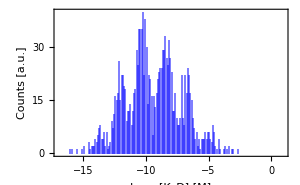

```mathematica
n7=Histogram[{Log10[ktab7]},{0.1},Frame->True,ChartStyle->Blue,FrameLabel->{"Log_10[K_D] [M]","Counts [a.u.]"},ImageSize->300,PlotRange->{{-17,1},All}]
```

```mathematica
(* Analogous calculation for seed length 6 *)
```

```mathematica
AbsoluteTiming[SetSharedVariable[ktab6,ktab6i];
ktab6={};
ktab6i={};
ParallelDo[
AppendTo[ktab6,
ran={#}&/@RandomSample[Range[1,7],1];Exp[ToExpression[TextCases[RunProcess[$SystemShell,"StandardOutput",comm<>StringJoin[up[[ii,1]],StringJoin[Delete[StringPartition[seeds[[sd]],1,1],ran]],up[[jj,1]]]<>"&"<>StringJoin[up[[jj,2]],StringJoin[Delete[StringPartition[pseeds[[sd]],1,1],-ran]],up[[ii,2]]]<>"'"],"Word"][[2]]]/0.593]];
AppendTo[ktab6i,{{Count[Delete[StringPartition[seeds[[sd]],1,1],ran],"A"],Count[Delete[StringPartition[seeds[[sd]],1,1],ran],"U"],Count[Delete[StringPartition[seeds[[sd]],1,1],ran],"C"],Count[Delete[StringPartition[seeds[[sd]],1,1],ran],"G"]}}];
,{ii,1,Length[up]},{jj,1,Length[up]},{sd,Table[RandomInteger[{1,Length[seeds]}],{NSEED}]}];]
```

{17.0488,Null}

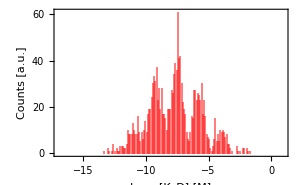

```mathematica
n6=Histogram[{Log10[ktab6]},{0.1},Frame->True,ChartStyle->Red,FrameLabel->{"Log_10[K_D] [M]","Counts [a.u.]"},ImageSize->300,PlotRange->{{-17,1},All}]
```

```mathematica
(* Analogous calculation for seed length 5 *)
```

```mathematica
AbsoluteTiming[SetSharedVariable[ktab5,ktab5i];
ktab5={};
ktab5i={};
ParallelDo[
AppendTo[ktab5,
ran={#}&/@RandomSample[Range[1,7],2];Exp[ToExpression[TextCases[RunProcess[$SystemShell,"StandardOutput",comm<>StringJoin[up[[ii,1]],StringJoin[Delete[StringPartition[seeds[[sd]],1,1],ran]],up[[jj,1]]]<>"&"<>StringJoin[up[[jj,2]],StringJoin[Delete[StringPartition[pseeds[[sd]],1,1],-ran]],up[[ii,2]]]<>"'"],"Word"][[2]]]/0.593]];
AppendTo[ktab5i,{{Count[Delete[StringPartition[seeds[[sd]],1,1],ran],"A"],Count[Delete[StringPartition[seeds[[sd]],1,1],ran],"U"],Count[Delete[StringPartition[seeds[[sd]],1,1],ran],"C"],Count[Delete[StringPartition[seeds[[sd]],1,1],ran],"G"]}}];
,{ii,1,Length[up]},{jj,1,Length[up]},{sd,Table[RandomInteger[{1,Length[seeds]}],{NSEED}]}];]
```

{17.3452,Null}

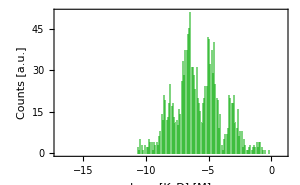

```mathematica
n5=Histogram[{Log10[ktab5]},{0.1},Frame->True,ChartStyle->Darker[Green],FrameLabel->{"Log_10[K_D] [M]","Counts [a.u.]"},ImageSize->300,PlotRange->{{-17,1},All}]
```